```mathematica
WienerProcess[0,1]
```

WienerProcess[0,1]

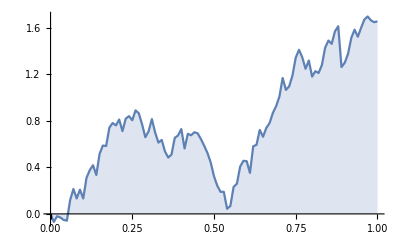

```mathematica
ListLinePlot[data,Filling->Axis]
```

```mathematica
ClearAll
```

```mathematica
Clear[data]
```

```mathematica
data :=RandomFunction[WienerProcess[0,1],{0,1,0.01}][[2]][[1]]//Flatten;
stoppingtime[H_,X_]:= Min[Position[Table[Boole[TrueQ[X[[i]]<H]]1,{i,1,Length[data]}],1]];
h:= Table[X=data;Table[If[i<stoppingtime[-1,X],X[[i]],-2],{i,1,Length[data]}],{14}]
```

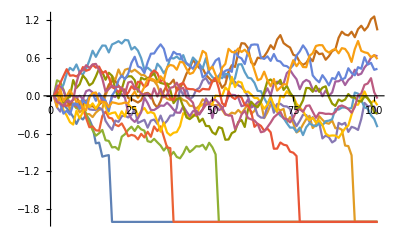

```mathematica
ListLinePlot[h]
```